```mathematica
RichSty[Leg_,fs_,thick_,ff_]:={LabelStyle->Directive[fs,Black,(FontFamily->ff)],BaseStyle->{FontFamily->"Times",FontSize->fs},FrameLabel->Leg,Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[thick]],FrameTicksStyle->Directive[fs]};
```

## Fourier transformation

```mathematica
(*SDataOrg: signal,  tTable: corresponding times *)
(*T: Final Time, NN: Steps*)
FourierTransformation[SDataOrg_,tTable_,T_,NN_]:=Block[{ReSData,ImSData,ReSInterpol,ImSInterpol,SDataNew,FourierData,AwData,AwDataRe,AwDataAbs,AwDataIm},
ReSData=ParallelTable[{tTable[[i]],Re@SDataOrg[[i]]},{i,1,Length@SDataOrg}];
ImSData=ParallelTable[{tTable[[i,1]],Im@SDataOrg[[i]]},{i,1,Length@SDataOrg}];

ReSInterpol=Interpolation[ReSData,InterpolationOrder->3];
ImSInterpol=Interpolation[ImSData,InterpolationOrder->3];

SDataNew=ParallelTable[(ReSInterpol[(r-1)/NN T]+ⅈ ImSInterpol[(r-1)/NN T])Exp[-ⅈ π (r-1)],{r,1,NN}];
FourierData=Fourier[SDataNew,FourierParameters->{-1,1}];
AwData=ParallelTable[{-NN π/T+(s-1)(2π)/T, T FourierData[[s]]},{s,1,NN}];
AwDataRe=ParallelTable[{AwData[[i,1]], Re@AwData[[i,2]]},{i,1,Length@AwData}];
AwDataIm=ParallelTable[{AwData[[i,1]], Im@AwData[[i,2]]},{i,1,Length@AwData}];
AwDataAbs=ParallelTable[{AwData[[i,1]], Abs@AwData[[i,2]]},{i,1,Length@AwData}];
{AwDataRe,AwDataIm,AwDataAbs}

]
```

```mathematica
(*SDataOrg: signal,  tTable: corresponding times *)
(*T: Final Time, NN: Steps*)
(*FourierTransformationFromInterpol[ReSInterpol_,ImSInterpol_,T_,NN_]:=Block[{ReSData,ImSData,SDataNew,FourierData,AwData,AwDataRe,AwDataAbs,AwDataIm},

SDataNew=Table[(ReSInterpol[(r-1)/NN T]+ⅈ ImSInterpol[(r-1)/NN T])Exp[-ⅈ π (r-1)],{r,1,NN}];
FourierData=Fourier[SDataNew,FourierParameters->{-1,1}];
AwData=Table[{-NN π/T+(s-1)(2π)/T, T FourierData[[s]]},{s,1,NN}];
AwDataRe=Table[{AwData[[i,1]], Re@AwData[[i,2]]},{i,1,Length@AwData}];
AwDataIm=Table[{AwData[[i,1]], Im@AwData[[i,2]]},{i,1,Length@AwData}];
AwDataAbs=Table[{AwData[[i,1]], Abs@AwData[[i,2]]},{i,1,Length@AwData}];
{AwDataRe,AwDataIm,AwDataAbs}

]*)
```

```mathematica
(*SDataOrg: signal,  tTable: corresponding times *)
(*T: Final Time, NN: Steps*)
FourierTransformationFromInterpol[ReSInterpol_,ImSInterpol_,T_,NN_]:=Block[{ReSData,ImSData,SDataNew,FourierData,AwData,AwDataRe,rTable,SDataNew2,AwDataAbs,AwDataIm,interpol,xTable},
interpol[r_]:=(ReSInterpol[(r-1)/NN T]+ⅈ ImSInterpol[(r-1)/NN T])Exp[-ⅈ π (r-1)];
(*Print["1"];
Print[interpol[10]];*)
rTable=Range[NN]//N;
(*Print[interpol[4]];*)
SDataNew=interpol[rTable];
(*SDataNew=ParallelTable[(ReSInterpol[(r-1)/NN T]+ⅈ ImSInterpol[(r-1)/NN T])Exp[-ⅈ π (r-1)],{r,1,NN}];*)
(*Print[SDataNew2-SDataNew];*)
(*Print["2"];*)
(*Print[SDataNew];*)
FourierData=T Fourier[SDataNew,FourierParameters->{-1,1}];
(*Print["3"];*)

xTable=-NN π/T+(rTable-1)(2π)/T;
AwData={xTable,FourierData}ᵀ;
(*AwData=Table[{-NN π/T+(s-1)(2π)/T, T FourierData[[s]]},{s,1,NN}];
Print[AwData-AwData2];*)
AwDataRe={xTable,Re[FourierData]}ᵀ;
AwDataIm={xTable,Im[FourierData]}ᵀ;
AwDataAbs={xTable,Abs[ FourierData]}ᵀ;

(*AwDataRe=Table[{AwData[[i,1]], Re@AwData[[i,2]]},{i,1,Length@AwData}];
AwDataIm=Table[{AwData[[i,1]], Im@AwData[[i,2]]},{i,1,Length@AwData}];
AwDataAbs=Table[{AwData[[i,1]], Abs@AwData[[i,2]]},{i,1,Length@AwData}];*)
{AwDataRe,AwDataIm,AwDataAbs}

]
```

## Spectrum from S(t),

### run 2

```mathematica
folder0=NotebookDirectory[];
folder=folder0<>"/run_2/"
SetDirectory[folder];
Name=FileNames[];
```

/Users/yes/Documents/Scientific_Projects/Variational_approaches/genPolaron/mm//run_2/

```mathematica
data={};
Do[
data=Join[data,Import[Name[[n]]]];
,{n,2,Length[Name]}]
```

```mathematica
tTable=Transpose[data][[1]];
ReSTable=Transpose[data][[2]];
ImSTable=Transpose[data][[3]];
```

P: 0. tEnd: 56.5764

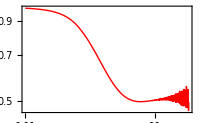

P: 0.088 tEnd: 56.5764

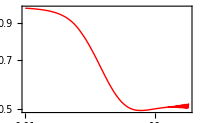

P: 0.18 tEnd: 56.6324

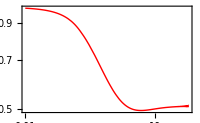

P: 0.26 tEnd: 56.7561

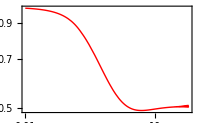

P: 0.35 tEnd: 56.9579

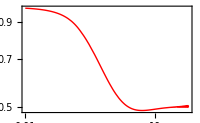

P: 0.44 tEnd: 58.0634

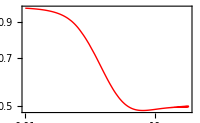

P: 0.53 tEnd: 56.7956

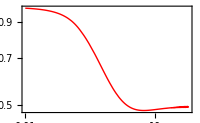

P: 0.62 tEnd: 58.0798

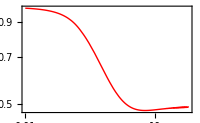

P: 0.71 tEnd: 56.9532

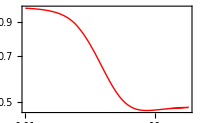

P: 0.79 tEnd: 56.7302

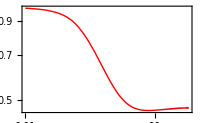

P: 0.88 tEnd: 56.5739

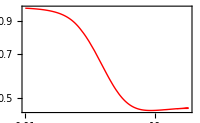

P: 0.97 tEnd: 50.3999

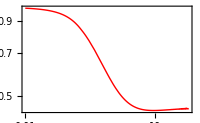

P: 1.1 tEnd: 13.252

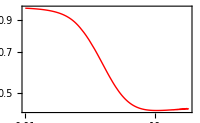

P: 1.1 tEnd: 54.7098

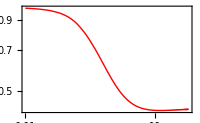

P: 1.2 tEnd: 56.6209

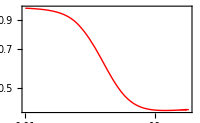

P: 1.3 tEnd: 56.7935

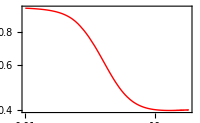

P: 1.4 tEnd: 57.0228

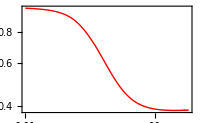

P: 1.5 tEnd: 58.2852

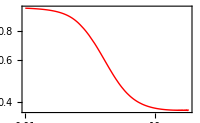

P: 1.6 tEnd: 56.6723

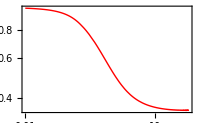

P: 1.7 tEnd: 57.059

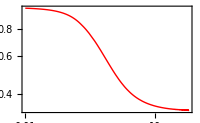

P: 1.8 tEnd: 55.4222

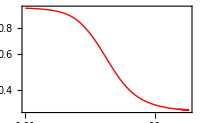

P: 1.9 tEnd: 56.9354

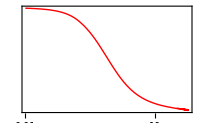

P: 1.9 tEnd: 51.962

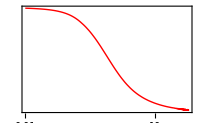

P: 2. tEnd: 56.8637

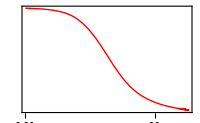

P: 2.1 tEnd: 58.5772

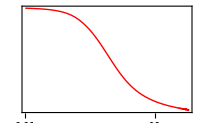

P: 2.2 tEnd: 56.8627

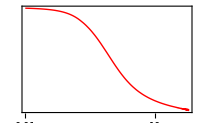

InterpolatingFunction::dmval: Input value {63.1959} lies outside the range of data in the interpolating function. Extrapolation will be used.

P: 2.3 tEnd: 57.4981

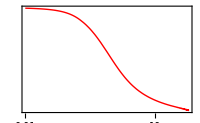

P: 2.4 tEnd: 56.9355

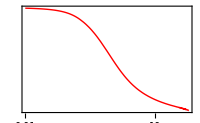

P: 2.5 tEnd: 56.3135

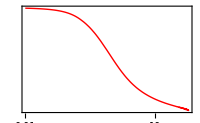

P: 2.6 tEnd: 56.9844

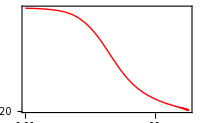

P: 2.6 tEnd: 56.2728

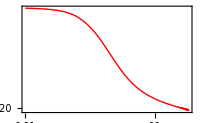

P: 2.7 tEnd: 56.9747

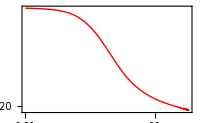

P: 2.8 tEnd: 51.6328

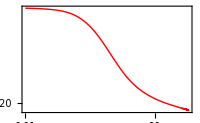

P: 2.9 tEnd: 56.9811

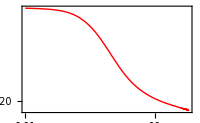

P: 3. tEnd: 52.8403

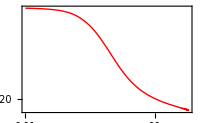

P: 3.1 tEnd: 56.9792

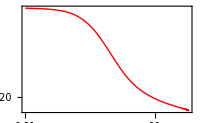

P: 3.2 tEnd: 52.4658

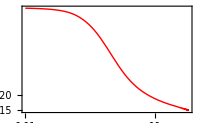

P: 3.3 tEnd: 56.9481

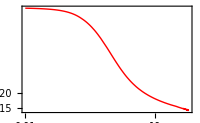

InterpolatingFunction::dmval: Input value {119.578} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {63.1723} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

P: 3.4 tEnd: 59.8741

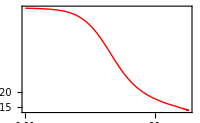

P: 3.4 tEnd: 56.8604

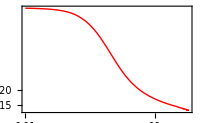

```mathematica
Name=FileNames[];


tDecay=100000;
wrange={-5,10};
DensityTable=Table[0,{0}];
spectab=Table[0,{0}];

For[ii=2,ii≤Length@Name,ii++,

data0=Import[Name[[ii]]];
tTable=Transpose[data0][[2]];
tmax=Max[tTable];
acur=-2;

ReSTable=Transpose[data0][[3]];
ImSTable=Transpose[data0][[4]];
STable=ReSTable + ⅈ *ImSTable;
AbsSTable=Abs[STable];

ReSInterpol=Interpolation[ReSTable];
ImSInterpol=Interpolation[ImSTable];
AbsSInterpol=Interpolation[AbsSTable];

ReSTableDec=Table[{tTable[[i]],Re[STable[[i]]]Exp[-tTable[[i]]/tDecay]},{i,1,Length@tTable}];
ImSTableDec=Table[{tTable[[i]],Im[STable[[i]]]Exp[-tTable[[i]]/tDecay]},{i,1,Length@tTable}];
AbsSTableDec=Table[{tTable[[i]],Abs[STable[[i]]]Exp[-tTable[[i]]/tDecay]},{i,1,Length@tTable}];

ReSInterpolExDec=Interpolation[ReSTableDec];
ImSInterpolExDec=Interpolation[ImSTableDec];
AbsSInterpolExDec=Interpolation[AbsSTableDec];

St=LogLogPlot[Abs@(AbsSInterpolExDec[t]),{t,0.01,tmax},Frame->True,PlotRange->All,PlotStyle->{Red},PlotPoints->15,MaxRecursion->6];
(*ReImSt=Plot[{Arg[ReSInterpolExDec[t]+ⅈ*ImSInterpolExDec[t]]},{t,0.01,tmax},Frame->True,PlotRange->All,PlotStyle->{Red,Blue},PlotPoints->15,MaxRecursion->6];*)
Print["P: ", N[data0[[1,1]],2], " tEnd: ", tEnd];
Print[Show[St,ImageSize->200]];
(*Print[Show[ReImSt,ImageSize->200]];*)

tEnd=t/.FindRoot[ImSInterpolExDec[t],{t,0.95tmax}];

If[tEnd>tmax,tEnd=tmax];

res=FourierTransformationFromInterpol[ReSInterpolExDec,ImSInterpolExDec,tEnd,2^14][[1]]//Quiet;
fullres=FourierTransformationFromInterpol[ReSInterpolExDec,ImSInterpolExDec,tEnd,2^14][[1;;2]]//Quiet;

LinResSingleStep=Table[{res[[i,1]],1/π Re@res[[i,2]]},{i,1,Length@res}];
int=Interpolation[LinResSingleStep,InterpolationOrder->1];
(*spec=Plot[int[w],{w,wrange[[1]],wrange[[2]]},Frame->True,PlotRange->All,PlotStyle->{Red},PlotPoints->15,MaxRecursion->6];*)
(*Print[Show[spec]];*)
data=Cases[spec,Line[data_]:>data,-4,1][[1]];
(*Print["P: ", N[data0[[1,1]],2], " tEnd: ", tEnd];*)
(*Print[Show[spec,ImageSize->200]];*)
AppendTo[spectab,int];
AppendTo[DensityTable,Table[{data0[[1,1]],data[[i,1]],data[[i,2]]},{i,1,Length@data}]];

retab=fullres[[1,All]];
reint=Interpolation[retab];
imtab=fullres[[2,All]];
imint=Interpolation[imtab];
(*Print["P: ", N[data0[[1,1]],2], " tEnd: ", tEnd];
Print[Plot[{Re[ⅈ/(reint[w]+ⅈ imint[w])],Im[ⅈ/(reint[w]+ⅈ imint[w])]},{w,-5,10},PlotRange->All]];*)

];
DensityTable=Flatten[DensityTable,1];
```

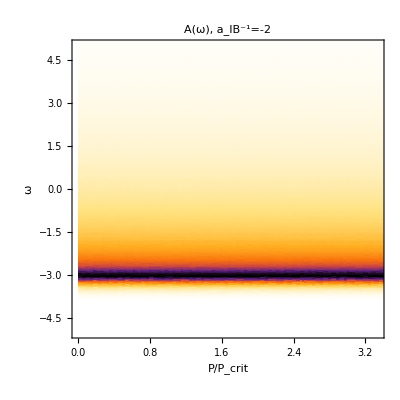

```mathematica
PlotSpec2=Show[ListDensityPlot[DensityTable,PlotRange->{{0,3.34},{-5,5},All},InterpolationOrder->1,ColorFunction->(ColorData[{"SunsetColors","Reverse"}]),ClippingStyle->Automatic,ColorFunctionScaling->{-0.01,1}],AspectRatio->1,PlotRangeClipping->True,PlotRangePadding->None,RichSty[{"P/P_crit","ω"},14,0.0036,"Times"],PlotLabel->"A(ω), a_IB^-1=-2"]
```

```mathematica
Export["PlotSpec2.pdf",PlotSpec2]
```

PlotSpec2.pdf

```mathematica
DensityTable
```

{{0.,-10.,0.00219575},{0.,-9.97853,0.0021993},{0.,-9.95706,0.00220285},«14064»,{3.44271483691331603,9.97687,0.0164009},{3.44271483691331603,10.,0.0163045}}

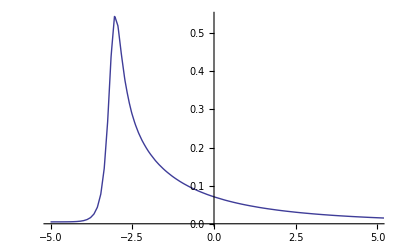

```mathematica
n=24;
ListPlot[Sort[Transpose[Drop[Transpose[Take[DensityTable,{300*n+1,300*(n+1)}]],1]],#1[[1]]<#2[[1]]&],PlotRange->{{-5,5},All},Joined->True]
```

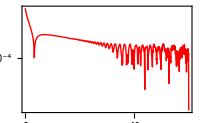
```mathematica
Show[-Graphics-,LogPlot[0.009Exp[-x*0.08],{x,0.1,60}]]
```

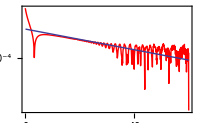

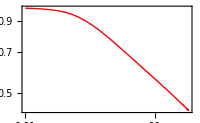
```mathematica
Show[-Graphics-,LogLogPlot[0.77x^-0.14,{x,0.1,60}]]
```

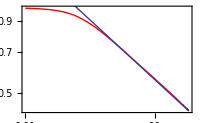

### run 2: dissipation

```mathematica
folder0=NotebookDirectory[];
folder=folder0<>"run_2/"
SetDirectory[folder];
Name=FileNames[]
```

/Users/yes/Documents/Scientific_Projects/Variational_approaches/genPolaron/mm/run_2/

{.DS_Store,gquench_aIBi_-2.00_P_0.00.dat,gquench_aIBi_-2.00_P_0.09.dat,gquench_aIBi_-2.00_P_0.18.dat,gquench_aIBi_-2.00_P_0.26.dat,gquench_aIBi_-2.00_P_0.35.dat,gquench_aIBi_-2.00_P_0.44.dat,gquench_aIBi_-2.00_P_0.53.dat,gquench_aIBi_-2.00_P_0.62.dat,gquench_aIBi_-2.00_P_0.71.dat,gquench_aIBi_-2.00_P_0.79.dat,gquench_aIBi_-2.00_P_0.88.dat,gquench_aIBi_-2.00_P_0.97.dat,gquench_aIBi_-2.00_P_1.06.dat,gquench_aIBi_-2.00_P_1.15.dat,gquench_aIBi_-2.00_P_1.24.dat,gquench_aIBi_-2.00_P_1.32.dat,gquench_aIBi_-2.00_P_1.41.dat,gquench_aIBi_-2.00_P_1.50.dat,gquench_aIBi_-2.00_P_1.59.dat,gquench_aIBi_-2.00_P_1.68.dat,gquench_aIBi_-2.00_P_1.77.dat,gquench_aIBi_-2.00_P_1.85.dat,gquench_aIBi_-2.00_P_1.94.dat,gquench_aIBi_-2.00_P_2.03.dat,gquench_aIBi_-2.00_P_2.12.dat,gquench_aIBi_-2.00_P_2.21.dat,gquench_aIBi_-2.00_P_2.30.dat,gquench_aIBi_-2.00_P_2.38.dat,gquench_aIBi_-2.00_P_2.47.dat,gquench_aIBi_-2.00_P_2.56.dat,gquench_aIBi_-2.00_P_2.65.dat,gquench_aIBi_-2.00_P_2.74.dat,gquench_aIBi_-2.00_P_2.82.dat,gquench_aIBi_-2.00_P_2.91.dat,gquench_aIBi_-2.00_P_3.00.dat,gquench_aIBi_-2.00_P_3.09.dat,gquench_aIBi_-2.00_P_3.18.dat,gquench_aIBi_-2.00_P_3.27.dat,gquench_aIBi_-2.00_P_3.35.dat,gquench_aIBi_-2.00_P_3.44.dat}

```mathematica
data={};
Do[
data=Join[data,Import[Name[[n]]]];
,{n,2,Length[Name]}]
```

```mathematica
tTable=Transpose[data][[1]];
ReSTable=Transpose[data][[2]];
ImSTable=Transpose[data][[3]];
```

```mathematica
Name=FileNames[];


tDecay=3;
wrange={-10,10};
DensityTable=Table[0,{0}];
spectab=Table[0,{0}];
PowerTable={};
For[ii=2,ii≤Length@Name,ii++,

data0=Import[Name[[ii]]];
tTable=Transpose[data0][[2]];
tmax=Max[tTable];
acur=-2;
ReSTable=Transpose[data0][[3]];
ImSTable=Transpose[data0][[4]];
STable=ReSTable + ⅈ *ImSTable;
AbsSTable=Abs[STable];
ReSInterpol=Interpolation[ReSTable];
ImSInterpol=Interpolation[ImSTable];
AbsSInterpol=Interpolation[AbsSTable];
ReSTableDec=Table[{tTable[[i]],Re[STable[[i]]]Exp[-tTable[[i]]/tDecay]},{i,1,Length@tTable}];
ImSTableDec=Table[{tTable[[i]],Im[STable[[i]]]Exp[-tTable[[i]]/tDecay]},{i,1,Length@tTable}];
AbsSTableDec=Table[{tTable[[i]],Abs[STable[[i]]]},{i,1,Length@tTable}];
FitAbs=FindFit[Take[AbsSTableDec,-300],{a*t^-b},{a,b},t];
PowerTable=AppendTo[PowerTable,{data0[[1,1]],b/.FitAbs}];

ReSInterpolExDec=Interpolation[ReSTableDec];
ImSInterpolExDec=Interpolation[ImSTableDec];
AbsSInterpolExDec=Interpolation[AbsSTableDec];
(*St=LogLogPlot[AbsSInterpolExDec[t],{t,0.01,tmax},Frame->True,PlotRange->All,PlotStyle->{Red},PlotPoints->15,MaxRecursion->6];*)
(*Print["P: ", N[data0[[1,1]],2], " tEnd: ", tEnd];
Print[Show[St,ImageSize->200]];*)


tEnd=t/.FindRoot[ImSInterpolExDec[t],{t,0.95tmax}];

If[tEnd>tmax,tEnd=tmax];

res=FourierTransformationFromInterpol[ReSInterpolExDec,ImSInterpolExDec,tEnd,2^14][[1]]//Quiet;
fullres=FourierTransformationFromInterpol[ReSInterpolExDec,ImSInterpolExDec,tEnd,2^14][[1;;2]]//Quiet;

LinResSingleStep=Table[{res[[i,1]],1/π Re@res[[i,2]]},{i,1,Length@res}];
int=Interpolation[LinResSingleStep,InterpolationOrder->1];
spec=Plot[int[w],{w,wrange[[1]],wrange[[2]]},Frame->True,PlotRange->All,PlotStyle->{Red},PlotPoints->15,MaxRecursion->6];
(*Print[Show[spec]];*)
data=Cases[spec,Line[data_]:>data,-4,1][[1]];
(*Print["P: ", N[data0[[1,1]],2], " tEnd: ", tEnd];*)
(*Print[Show[spec,ImageSize->200]];*)
AppendTo[spectab,int];
AppendTo[DensityTable,Table[{data0[[1,1]],data[[i,1]],data[[i,2]]},{i,1,Length@data}]];

retab=fullres[[1,All]];
reint=Interpolation[retab];
imtab=fullres[[2,All]];
imint=Interpolation[imtab];
(*Print["P: ", N[data0[[1,1]],2], " tEnd: ", tEnd];
Print[Plot[{Re[ⅈ/(reint[w]+ⅈ imint[w])],Im[ⅈ/(reint[w]+ⅈ imint[w])]},{w,-5,10},PlotRange->All]];*)

];
DensityTable=Flatten[DensityTable,1];
```

InterpolatingFunction::dmval: Input value {61.0509} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {322.98} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {84.1758} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

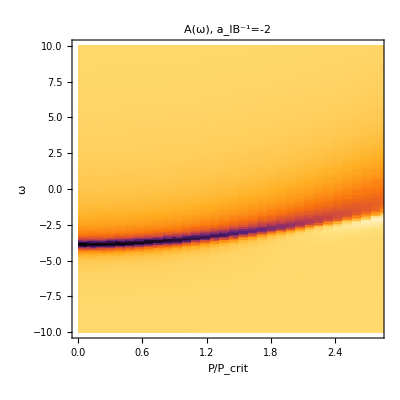

```mathematica
PlotSpec2=Show[ListDensityPlot[DensityTable,PlotRange->{{0,2.8},{wrange[[1]],wrange[[2]]},All},InterpolationOrder->1,ColorFunction->(ColorData[{"SunsetColors","Reverse"}]),ClippingStyle->Automatic,ColorFunctionScaling->{-0.01,1}],AspectRatio->1,PlotRangeClipping->True,PlotRangePadding->None,RichSty[{"P/P_crit","ω"},14,0.0036,"Times"],PlotLabel->"A(ω), a_IB^-1=-2"]
```

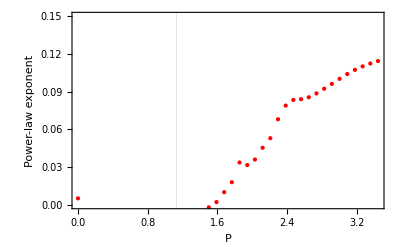

```mathematica
Show[ListPlot[PowerTable,PlotRange->{All,{0,0.15}},PlotStyle->Red],RichSty[{"P","Power-law exponent"},14,0.0036,"Times"],GridLines->{{1.1295513475243855},None}]
```

### run 3

```mathematica
folder0=NotebookDirectory[];
folder=folder0<>"run_3/"
SetDirectory[folder];
Name=FileNames[];
```

/Users/yes/Documents/Scientific_Projects/Variational_approaches/genPolaron/mm/run_3/

```mathematica
data={};
Do[
data=Join[data,Import[Name[[n]]]];
,{n,Length[Name]}]
```

```mathematica
tTable=Transpose[data][[1]];
ReSTable=Transpose[data][[2]];
ImSTable=Transpose[data][[3]];
```

```mathematica
Name=FileNames[];


tDecay=10;
wrange={-10,10};
DensityTable=Table[0,{0}];
spectab=Table[0,{0}];

For[ii=1,ii≤Length@Name,ii++,

data0=Import[Name[[ii]]];
tTable=Transpose[data0][[2]];
tmax=Max[tTable];
acur=-2;
ReSTable=Transpose[data0][[3]];
ImSTable=Transpose[data0][[4]];
STable=ReSTable + ⅈ *ImSTable;
ReSInterpol=Interpolation[ReSTable];
ImSInterpol=Interpolation[ImSTable];

ReSTableDec=Table[{tTable[[i]],Re[STable[[i]]]Exp[-tTable[[i]]/tDecay]},{i,1,Length@tTable}];
ImSTableDec=Table[{tTable[[i]],Im[STable[[i]]]Exp[-tTable[[i]]/tDecay]},{i,1,Length@tTable}];
ReSInterpolExDec=Interpolation[ReSTableDec];
ImSInterpolExDec=Interpolation[ImSTableDec];

tEnd=t/.FindRoot[ImSInterpolExDec[t],{t,0.95tmax}];

If[tEnd>tmax,tEnd=tmax];

res=FourierTransformationFromInterpol[ReSInterpolExDec,ImSInterpolExDec,tEnd,2^14][[1]]//Quiet;
fullres=FourierTransformationFromInterpol[ReSInterpolExDec,ImSInterpolExDec,tEnd,2^14][[1;;2]]//Quiet;

LinResSingleStep=Table[{res[[i,1]],1/π Re@res[[i,2]]},{i,1,Length@res}];
int=Interpolation[LinResSingleStep,InterpolationOrder->1];
spec=Plot[int[w],{w,wrange[[1]],wrange[[2]]},Frame->True,PlotRange->All,PlotStyle->{Red},PlotPoints->15,MaxRecursion->6];
(*Print[Show[spec]];*)
data=Cases[spec,Line[data_]:>data,-4,1][[1]];
(*Print["P: ", N[data0[[1,1]],2], " tEnd: ", tEnd];
Print[Show[spec,ImageSize->200]];*)
AppendTo[spectab,int];
AppendTo[DensityTable,Table[{data0[[1,1]],data[[i,1]],data[[i,2]]},{i,1,Length@data}]];

retab=fullres[[1,All]];
reint=Interpolation[retab];
imtab=fullres[[2,All]];
imint=Interpolation[imtab];
(*Print[Plot[{Re[ⅈ/(reint[w]+ⅈ imint[w])],Im[ⅈ/(reint[w]+ⅈ imint[w])]},{w,-10,10},PlotRange->All]];*)

];
DensityTable=Flatten[DensityTable,1];
```

InterpolatingFunction::dmval: Input value {69.8957} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {60.7674} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

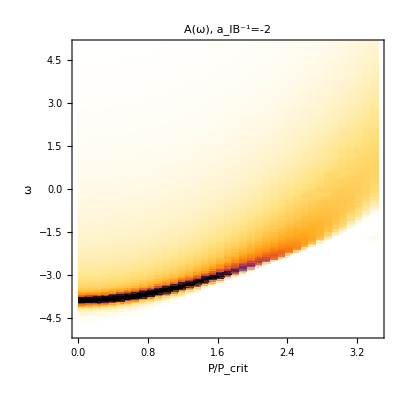

```mathematica
Show[ListDensityPlot[DensityTable,PlotRange->{{0,3.44},{-5,5},{0,1.}},InterpolationOrder->1,ColorFunction->(ColorData[{"SunsetColors","Reverse"}]),ClippingStyle->Automatic,ColorFunctionScaling->{-0.01,1}],AspectRatio->1,PlotRangeClipping->True,PlotRangePadding->None,RichSty[{"P/P_crit","ω"},14,0.0036,"Times"],PlotLabel->"A(ω), a_IB^-1=-2"]
```

```mathematica
DensityTable
```

{{0.,-10.,0.00219575},{0.,-9.97853,0.0021993},{0.,-9.95706,0.00220285},«14064»,{3.44271483691331603,9.97687,0.0164009},{3.44271483691331603,10.,0.0163045}}

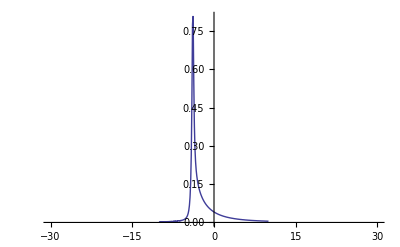

```mathematica
n=0;
ListPlot[Sort[Transpose[Drop[Transpose[Take[DensityTable,{600*n+1,600*(n+1)}]],1]],#1[[1]]<#2[[1]]&],PlotRange->{{-30,30},All},Joined->True]
```

### run 4

```mathematica
folder0=NotebookDirectory[];
folder=folder0<>"run_4/"
SetDirectory[folder];
Name=FileNames[]
```

/Users/yes/Documents/Scientific_Projects/Variational_approaches/genPolaron/mm/run_4/

{gquench_aIBi_-4.00_P_0.00.dat,gquench_aIBi_-4.00_P_0.07.dat,gquench_aIBi_-4.00_P_0.14.dat,gquench_aIBi_-4.00_P_0.21.dat,gquench_aIBi_-4.00_P_0.29.dat,gquench_aIBi_-4.00_P_0.36.dat,gquench_aIBi_-4.00_P_0.43.dat,gquench_aIBi_-4.00_P_0.50.dat,gquench_aIBi_-4.00_P_0.57.dat,gquench_aIBi_-4.00_P_0.64.dat,gquench_aIBi_-4.00_P_0.71.dat,gquench_aIBi_-4.00_P_0.79.dat,gquench_aIBi_-4.00_P_0.86.dat,gquench_aIBi_-4.00_P_0.93.dat,gquench_aIBi_-4.00_P_1.00.dat,gquench_aIBi_-4.00_P_1.07.dat,gquench_aIBi_-4.00_P_1.14.dat,gquench_aIBi_-4.00_P_1.21.dat,gquench_aIBi_-4.00_P_1.29.dat,gquench_aIBi_-4.00_P_1.36.dat,gquench_aIBi_-4.00_P_1.43.dat,gquench_aIBi_-4.00_P_1.50.dat,gquench_aIBi_-4.00_P_1.57.dat,gquench_aIBi_-4.00_P_1.64.dat,gquench_aIBi_-4.00_P_1.71.dat,gquench_aIBi_-4.00_P_1.79.dat,gquench_aIBi_-4.00_P_1.86.dat,gquench_aIBi_-4.00_P_1.93.dat,gquench_aIBi_-4.00_P_2.00.dat,gquench_aIBi_-4.00_P_2.07.dat,gquench_aIBi_-4.00_P_2.14.dat,gquench_aIBi_-4.00_P_2.21.dat,gquench_aIBi_-4.00_P_2.29.dat,gquench_aIBi_-4.00_P_2.36.dat,gquench_aIBi_-4.00_P_2.43.dat,gquench_aIBi_-4.00_P_2.50.dat,gquench_aIBi_-4.00_P_2.57.dat,gquench_aIBi_-4.00_P_2.64.dat,gquench_aIBi_-4.00_P_2.71.dat,gquench_aIBi_-4.00_P_2.79.dat}

```mathematica
data={};
Do[
data=Join[data,Import[Name[[n]]]];
,{n,Length[Name]}]
```

```mathematica
tTable=Transpose[data][[1]];
ReSTable=Transpose[data][[2]];
ImSTable=Transpose[data][[3]];
```

```mathematica
Name=FileNames[];


tDecay=3;
wrange={-10,10};
DensityTable=Table[0,{0}];
spectab=Table[0,{0}];
PowerTable={};
ZTable={};
StTable3D={};
NphTable={};
For[ii=1,ii≤Length@Name,ii++,

data0=Import[Name[[ii]]];
tTable=Transpose[data0][[2]];
tmax=Max[tTable];
acur=-2;
ReSTable=Transpose[data0][[3]];
ImSTable=Transpose[data0][[4]];
STable=ReSTable + ⅈ *ImSTable;
AbsSTable=Abs[STable];
ReSInterpol=Interpolation[ReSTable];
ImSInterpol=Interpolation[ImSTable];
AbsSInterpol=Interpolation[AbsSTable];
ReSTableDec=Table[{tTable[[i]],Re[STable[[i]]]Exp[-tTable[[i]]/tDecay]},{i,1,Length@tTable}];
ImSTableDec=Table[{tTable[[i]],Im[STable[[i]]]Exp[-tTable[[i]]/tDecay]},{i,1,Length@tTable}];
AbsSTableDec=Table[{tTable[[i]],Abs[STable[[i]]]},{i,1,Length@tTable}];
FitAbs=FindFit[Take[AbsSTableDec,-300],{a*t^-b},{a,b},t];
PowerTable=AppendTo[PowerTable,{data0[[1,1]],b/.FitAbs}];
ZTable=AppendTo[ZTable,{data0[[1,1]],a/.FitAbs}];
StTable3D=AppendTo[StTable3D,Table[{data0[[1,1]],Log[AbsSTableDec[[i,1]]],Log[AbsSTableDec[[i,2]]]},{i,1,Length@AbsSTableDec}]];
NphTable=AppendTo[NphTable,Table[{AbsSTableDec[[i,1]],-2*Log[AbsSTableDec[[i,2]]]},{i,1,Length@AbsSTableDec}]];

ReSInterpolExDec=Interpolation[ReSTableDec];
ImSInterpolExDec=Interpolation[ImSTableDec];
AbsSInterpolExDec=Interpolation[AbsSTableDec];
(*St=LogLogPlot[AbsSInterpolExDec[t],{t,0.01,tmax},Frame->True,PlotRange->All,PlotStyle->{Red},PlotPoints->15,MaxRecursion->6];*)
(*Print["P: ", N[data0[[1,1]],2], " tEnd: ", tEnd];
Print[Show[St,ImageSize->200]];*)


tEnd=t/.FindRoot[ImSInterpolExDec[t],{t,0.95tmax}];

If[tEnd>tmax,tEnd=tmax];

res=FourierTransformationFromInterpol[ReSInterpolExDec,ImSInterpolExDec,tEnd,2^14][[1]]//Quiet;
fullres=FourierTransformationFromInterpol[ReSInterpolExDec,ImSInterpolExDec,tEnd,2^14][[1;;2]]//Quiet;

LinResSingleStep=Table[{res[[i,1]],1/π Re@res[[i,2]]},{i,1,Length@res}];
int=Interpolation[LinResSingleStep,InterpolationOrder->1];
spec=Plot[int[w],{w,wrange[[1]],wrange[[2]]},Frame->True,PlotRange->All,PlotStyle->{Red},PlotPoints->15,MaxRecursion->6];
(*Print[Show[spec]];*)
data=Cases[spec,Line[data_]:>data,-4,1][[1]];
(*Print["P: ", N[data0[[1,1]],2], " tEnd: ", tEnd];*)
(*Print[Show[spec,ImageSize->200]];*)
AppendTo[spectab,int];
AppendTo[DensityTable,Table[{data0[[1,1]],data[[i,1]],data[[i,2]]},{i,1,Length@data}]];

retab=fullres[[1,All]];
reint=Interpolation[retab];
imtab=fullres[[2,All]];
imint=Interpolation[imtab];
(*Print["P: ", N[data0[[1,1]],2], " tEnd: ", tEnd];
Print[Plot[{Re[ⅈ/(reint[w]+ⅈ imint[w])],Im[ⅈ/(reint[w]+ⅈ imint[w])]},{w,-5,10},PlotRange->All]];*)

];
DensityTable=Flatten[DensityTable,1];
```

InterpolatingFunction::dmval: Input value {61.0335} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {61.8271} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {68.2766} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

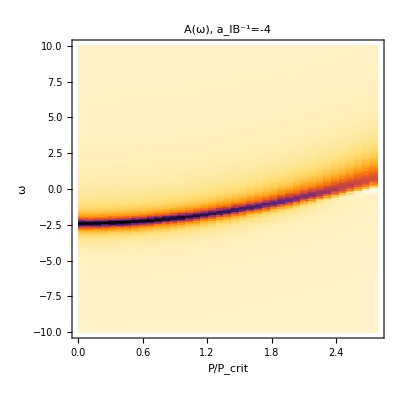

```mathematica
PlotSpec4=Show[ListDensityPlot[DensityTable,PlotRange->{{0,2.79},{wrange[[1]],wrange[[2]]},All},InterpolationOrder->1,ColorFunction->(ColorData[{"SunsetColors","Reverse"}]),ClippingStyle->Automatic,ColorFunctionScaling->{-0.01,1}],AspectRatio->1,PlotRangeClipping->True,PlotRangePadding->None,RichSty[{"P/P_crit","ω"},14,0.0036,"Times"],PlotLabel->"A(ω), a_IB^-1=-4"]
```

```mathematica
Export["/Users/yes/Downloads/Spectrum1.pdf",PlotSpec4,AspectRatio->0.7]
Export["/Users/yes/Dowloads/Spectrum1.png",PlotSpec4,AspectRatio->0.7]
```

/Users/yes/Downloads/Spectrum1.pdf

/Users/yes/Dowloads/Spectrum1.png

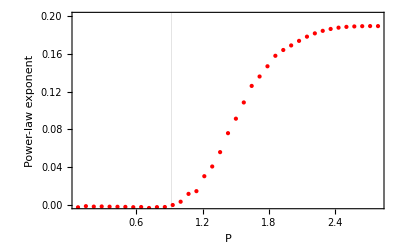

```mathematica
Show[ListPlot[PowerTable,PlotRange->{All,{0,0.2}},PlotStyle->Red],RichSty[{"P","Power-law exponent"},14,0.0036,"Times"],GridLines->{{0.9183624613615349},None}]
```

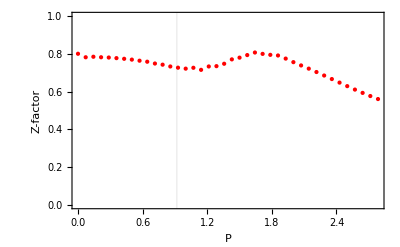

```mathematica
Show[ListPlot[{ZTable,Zdata},PlotRange->{All,{0,1}},PlotStyle->Red],RichSty[{"P","Z-factor"},14,0.0036,"Times"],GridLines->{{0.9183624613615349},None}]
```

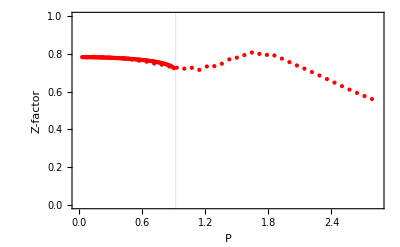

```mathematica
Show[ListPointPlot3D[Flatten[StTable3D,1]]]
```

-Graphics3D-

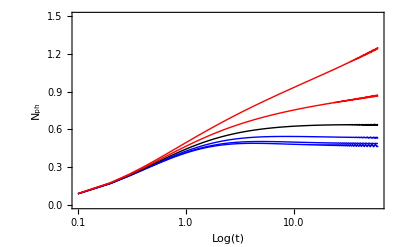

```mathematica
ListLogLinearPlot[Table[Table[{NphTable[[ii,i,1]],NphTable[[ii,i,2]]},{i,2,Length[NphTable[[ii]]]}],{ii,2,23,4}],PlotStyle->{Blue,Blue,Blue,{Black,Thick},Red,Red},PlotRange->{{0.1,60},{0,1.5}},Joined->True,RichSty[{"Log(t)","N_ph"},14,0.0036,"Times"]]
```

### run 5

```mathematica
folder0=NotebookDirectory[];
folder=folder0<>"run_5/"
SetDirectory[folder];
Name=FileNames[]
```

/Users/yes/Documents/Scientific_Projects/Variational_approaches/genPolaron/mm/run_5/

{.DS_Store,gquench_aIBi_2.50_P_0.00.dat,gquench_aIBi_2.50_P_0.24.dat,gquench_aIBi_2.50_P_0.49.dat,gquench_aIBi_2.50_P_0.73.dat,gquench_aIBi_2.50_P_0.97.dat,gquench_aIBi_2.50_P_1.22.dat,gquench_aIBi_2.50_P_1.46.dat,gquench_aIBi_2.50_P_1.70.dat,gquench_aIBi_2.50_P_1.94.dat,gquench_aIBi_2.50_P_2.19.dat,gquench_aIBi_2.50_P_2.43.dat,gquench_aIBi_2.50_P_2.67.dat,gquench_aIBi_2.50_P_2.92.dat,gquench_aIBi_2.50_P_3.16.dat,gquench_aIBi_2.50_P_3.40.dat,gquench_aIBi_2.50_P_3.65.dat,gquench_aIBi_2.50_P_3.89.dat,gquench_aIBi_2.50_P_4.13.dat,gquench_aIBi_2.50_P_4.38.dat,gquench_aIBi_2.50_P_4.62.dat,gquench_aIBi_2.50_P_4.86.dat,gquench_aIBi_2.50_P_5.11.dat,gquench_aIBi_2.50_P_5.35.dat,gquench_aIBi_2.50_P_5.59.dat,gquench_aIBi_2.50_P_5.83.dat,gquench_aIBi_2.50_P_6.08.dat,gquench_aIBi_2.50_P_6.32.dat,gquench_aIBi_2.50_P_6.56.dat,gquench_aIBi_2.50_P_6.81.dat,gquench_aIBi_2.50_P_7.05.dat,gquench_aIBi_2.50_P_7.29.dat,gquench_aIBi_2.50_P_7.54.dat,gquench_aIBi_2.50_P_7.78.dat,gquench_aIBi_2.50_P_8.02.dat,gquench_aIBi_2.50_P_8.27.dat,gquench_aIBi_2.50_P_8.51.dat,gquench_aIBi_2.50_P_8.75.dat,gquench_aIBi_2.50_P_9.00.dat,gquench_aIBi_2.50_P_9.24.dat,gquench_aIBi_2.50_P_9.48.dat}

```mathematica
data={};
Do[
data=Join[data,Import[Name[[n]]]];
,{n,2,Length[Name]}]
```

```mathematica
tTable=Transpose[data][[1]];
ReSTable=Transpose[data][[2]];
ImSTable=Transpose[data][[3]];
```

```mathematica
Name=FileNames[];


tDecay=3;
wrange={-20,20};
DensityTable=Table[0,{0}];
spectab=Table[0,{0}];
PowerTable={};

For[ii=2,ii≤Length@Name,ii++,

data0=Import[Name[[ii]]];
tTable=Transpose[data0][[2]];
tmax=Max[tTable];
acur=-2;
ReSTable=Transpose[data0][[3]];
ImSTable=Transpose[data0][[4]];
STable=ReSTable + ⅈ *ImSTable;
AbsSTable=Abs[STable];
ReSInterpol=Interpolation[ReSTable];
ImSInterpol=Interpolation[ImSTable];
AbsSInterpol=Interpolation[AbsSTable];
ReSTableDec=Table[{tTable[[i]],Re[STable[[i]]]Exp[-tTable[[i]]/tDecay]},{i,1,Length@tTable}];
ImSTableDec=Table[{tTable[[i]],Im[STable[[i]]]Exp[-tTable[[i]]/tDecay]},{i,1,Length@tTable}];
AbsSTableDec=Table[{tTable[[i]],Abs[STable[[i]]]},{i,1,Length@tTable}];
ReSInterpolExDec=Interpolation[ReSTableDec];
ImSInterpolExDec=Interpolation[ImSTableDec];
AbsSInterpolExDec=Interpolation[AbsSTableDec];
(*St=LogLogPlot[AbsSInterpolExDec[t],{t,0.01,tmax},Frame->True,PlotRange->All,PlotStyle->{Red},PlotPoints->15,MaxRecursion->6];*)
(*Print["P: ", N[data0[[1,1]],2], " tEnd: ", tEnd];
Print[Show[St,ImageSize->200]];*)
FitAbs=FindFit[Take[AbsSTableDec,-200],{a*t^-b},{a,b},t];
PowerTable=AppendTo[PowerTable,{data0[[1,1]],b/.FitAbs}];

tEnd=t/.FindRoot[ImSInterpolExDec[t],{t,0.95tmax}];

If[tEnd>tmax,tEnd=tmax];

res=FourierTransformationFromInterpol[ReSInterpolExDec,ImSInterpolExDec,tEnd,2^14][[1]]//Quiet;
fullres=FourierTransformationFromInterpol[ReSInterpolExDec,ImSInterpolExDec,tEnd,2^14][[1;;2]]//Quiet;

LinResSingleStep=Table[{res[[i,1]],1/π Re@res[[i,2]]},{i,1,Length@res}];
int=Interpolation[LinResSingleStep,InterpolationOrder->1];
spec=Plot[int[w],{w,wrange[[1]],wrange[[2]]},Frame->True,PlotRange->All,PlotStyle->{Red},PlotPoints->15,MaxRecursion->6];
(*Print[Show[spec]];*)
data=Cases[spec,Line[data_]:>data,-4,1][[1]];
(*Print["P: ", N[data0[[1,1]],2], " tEnd: ", tEnd];*)
(*Print[Show[spec,ImageSize->200]];*)
AppendTo[spectab,int];
AppendTo[DensityTable,Table[{data0[[1,1]],data[[i,1]],data[[i,2]]},{i,1,Length@data}]];

retab=fullres[[1,All]];
reint=Interpolation[retab];
imtab=fullres[[2,All]];
imint=Interpolation[imtab];
(*Print["P: ", N[data0[[1,1]],2], " tEnd: ", tEnd];
Print[Plot[{Re[ⅈ/(reint[w]+ⅈ imint[w])],Im[ⅈ/(reint[w]+ⅈ imint[w])]},{w,-5,10},PlotRange->All]];*)

];
DensityTable=Flatten[DensityTable,1];
```

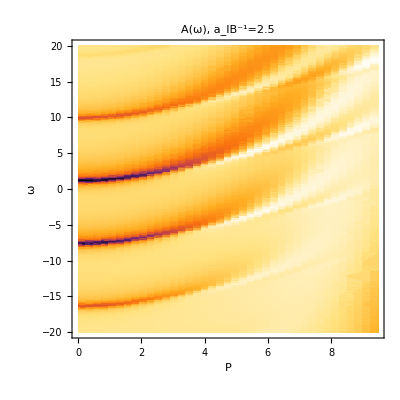

```mathematica
PlotSpec5=Show[ListDensityPlot[DensityTable,PlotRange->{{0,9.48},{wrange[[1]],wrange[[2]]},All},InterpolationOrder->1,ColorFunction->(ColorData[{"SunsetColors","Reverse"}]),ClippingStyle->Automatic,ColorFunctionScaling->{-0.01,1}],AspectRatio->1,PlotRangeClipping->True,PlotRangePadding->None,RichSty[{"P","ω"},14,0.0036,"Times"],PlotLabel->"A(ω), a_IB^-1=2.5"]
```

```mathematica
Export["/Users/yes/Dowloads/Spectrum2.pdf",-Graphics-,AspectRatio->0.7]
Export["/Users/yes/Dowloads/Spectrum2.png",-Graphics-,AspectRatio->0.7]
```

/Users/yes/Dowloads/Spectrum2.pdf

/Users/yes/Dowloads/Spectrum2.png

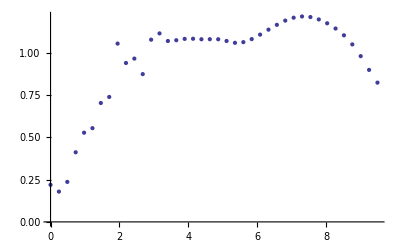

```mathematica
ListPlot[PowerTable]
```

### run 6

```mathematica
folder0=NotebookDirectory[];
folder=folder0<>"run_6/"
SetDirectory[folder];
Name=FileNames[]
```

/Users/yes/Documents/Scientific_Projects/Variational_approaches/genPolaron/mm/run_6/

{gquench_aIBi_4.50_P_0.00.dat,gquench_aIBi_4.50_P_0.09.dat,gquench_aIBi_4.50_P_0.18.dat,gquench_aIBi_4.50_P_0.26.dat,gquench_aIBi_4.50_P_0.35.dat,gquench_aIBi_4.50_P_0.44.dat,gquench_aIBi_4.50_P_0.53.dat,gquench_aIBi_4.50_P_0.62.dat,gquench_aIBi_4.50_P_0.70.dat,gquench_aIBi_4.50_P_0.79.dat,gquench_aIBi_4.50_P_0.88.dat,gquench_aIBi_4.50_P_0.97.dat,gquench_aIBi_4.50_P_1.06.dat,gquench_aIBi_4.50_P_1.14.dat,gquench_aIBi_4.50_P_1.23.dat,gquench_aIBi_4.50_P_1.32.dat,gquench_aIBi_4.50_P_1.41.dat,gquench_aIBi_4.50_P_1.50.dat,gquench_aIBi_4.50_P_1.59.dat,gquench_aIBi_4.50_P_1.67.dat,gquench_aIBi_4.50_P_1.76.dat,gquench_aIBi_4.50_P_1.85.dat,gquench_aIBi_4.50_P_1.94.dat,gquench_aIBi_4.50_P_2.03.dat,gquench_aIBi_4.50_P_2.11.dat,gquench_aIBi_4.50_P_2.20.dat,gquench_aIBi_4.50_P_2.29.dat,gquench_aIBi_4.50_P_2.38.dat,gquench_aIBi_4.50_P_2.47.dat,gquench_aIBi_4.50_P_2.55.dat,gquench_aIBi_4.50_P_2.64.dat,gquench_aIBi_4.50_P_2.73.dat,gquench_aIBi_4.50_P_2.82.dat,gquench_aIBi_4.50_P_2.91.dat,gquench_aIBi_4.50_P_2.99.dat,gquench_aIBi_4.50_P_3.08.dat,gquench_aIBi_4.50_P_3.17.dat,gquench_aIBi_4.50_P_3.26.dat,gquench_aIBi_4.50_P_3.35.dat,gquench_aIBi_4.50_P_3.43.dat}

```mathematica
data={};
Do[
data=Join[data,Import[Name[[n]]]];
,{n,Length[Name]}]
```

```mathematica
tTable=Transpose[data][[1]];
ReSTable=Transpose[data][[2]];
ImSTable=Transpose[data][[3]];
```

```mathematica
Name=FileNames[];


tDecay=3;
wrange={0,15};
DensityTable=Table[0,{0}];
spectab=Table[0,{0}];

For[ii=1,ii≤Length@Name,ii++,

data0=Import[Name[[ii]]];
tTable=Transpose[data0][[2]];
tmax=Max[tTable];
acur=-2;
ReSTable=Transpose[data0][[3]];
ImSTable=Transpose[data0][[4]];
STable=ReSTable + ⅈ *ImSTable;
AbsSTable=Abs[STable];
ReSInterpol=Interpolation[ReSTable];
ImSInterpol=Interpolation[ImSTable];
AbsSInterpol=Interpolation[AbsSTable];
ReSTableDec=Table[{tTable[[i]],Re[STable[[i]]]Exp[-tTable[[i]]/tDecay]},{i,1,Length@tTable}];
ImSTableDec=Table[{tTable[[i]],Im[STable[[i]]]Exp[-tTable[[i]]/tDecay]},{i,1,Length@tTable}];
AbsSTableDec=Table[{tTable[[i]],Abs[STable[[i]]]Exp[-tTable[[i]]/tDecay]},{i,1,Length@tTable}];
ReSInterpolExDec=Interpolation[ReSTableDec];
ImSInterpolExDec=Interpolation[ImSTableDec];
AbsSInterpolExDec=Interpolation[AbsSTableDec];
(*St=LogLogPlot[AbsSInterpolExDec[t],{t,0.01,tmax},Frame->True,PlotRange->All,PlotStyle->{Red},PlotPoints->15,MaxRecursion->6];*)
(*Print["P: ", N[data0[[1,1]],2], " tEnd: ", tEnd];
Print[Show[St,ImageSize->200]];*)

tEnd=t/.FindRoot[ImSInterpolExDec[t],{t,0.95tmax}];

If[tEnd>tmax,tEnd=tmax];

res=FourierTransformationFromInterpol[ReSInterpolExDec,ImSInterpolExDec,tEnd,2^14][[1]]//Quiet;
fullres=FourierTransformationFromInterpol[ReSInterpolExDec,ImSInterpolExDec,tEnd,2^14][[1;;2]]//Quiet;

LinResSingleStep=Table[{res[[i,1]],1/π Re@res[[i,2]]},{i,1,Length@res}];
int=Interpolation[LinResSingleStep,InterpolationOrder->1];
spec=Plot[int[w],{w,wrange[[1]],wrange[[2]]},Frame->True,PlotRange->All,PlotStyle->{Red},PlotPoints->15,MaxRecursion->6];
(*Print[Show[spec]];*)
data=Cases[spec,Line[data_]:>data,-4,1][[1]];
(*Print["P: ", N[data0[[1,1]],2], " tEnd: ", tEnd];*)
(*Print[Show[spec,ImageSize->200]];*)
AppendTo[spectab,int];
AppendTo[DensityTable,Table[{data0[[1,1]],data[[i,1]],data[[i,2]]},{i,1,Length@data}]];

retab=fullres[[1,All]];
reint=Interpolation[retab];
imtab=fullres[[2,All]];
imint=Interpolation[imtab];
(*Print["P: ", N[data0[[1,1]],2], " tEnd: ", tEnd];
Print[Plot[{Re[ⅈ/(reint[w]+ⅈ imint[w])],Im[ⅈ/(reint[w]+ⅈ imint[w])]},{w,-5,10},PlotRange->All]];*)

];
DensityTable=Flatten[DensityTable,1];
```

InterpolatingFunction::dmval: Input value {66.632} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {59.9848} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

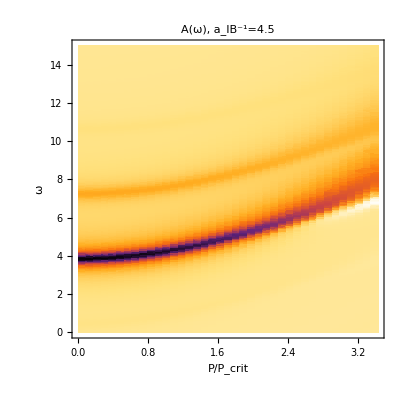

```mathematica
PlotSpec6=Show[ListDensityPlot[DensityTable,PlotRange->{{0,3.43},{wrange[[1]],wrange[[2]]},All},InterpolationOrder->1,ColorFunction->(ColorData[{"SunsetColors","Reverse"}]),ClippingStyle->Automatic,ColorFunctionScaling->{-0.01,1}],AspectRatio->1,PlotRangeClipping->True,PlotRangePadding->None,RichSty[{"P/P_crit","ω"},14,0.0036,"Times"],PlotLabel->"A(ω), a_IB^-1=4.5"]
```

### run 2: try to add a tail

```mathematica
folder0=NotebookDirectory[];
folder=folder0<>"/run_2/"
SetDirectory[folder];
Name=FileNames[];
```

/Users/yes/Documents/Scientific_Projects/Variational_approaches/genPolaron/mm//run_2/

```mathematica
data={};
Do[
data=Join[data,Import[Name[[n]]]];
,{n,2,Length[Name]}]
```

```mathematica
tTable=Transpose[data][[1]];
ReSTable=Transpose[data][[2]];
ImSTable=Transpose[data][[3]];
```

```mathematica
Name=FileNames[];


tDecay=4;
wrange={-5,10};
DensityTable=Table[0,{0}];
spectab=Table[0,{0}];

ii=20;

data0=Import[Name[[ii]]];
tTable=Transpose[data0][[2]];
tmax=Max[tTable];
acur=-2;

ReSTable=Transpose[data0][[3]];
ImSTable=Transpose[data0][[4]];
STable=ReSTable + ⅈ *ImSTable;
AbsSTable=Abs[STable];

ReSInterpol=Interpolation[ReSTable];
ImSInterpol=Interpolation[ImSTable];
AbsSInterpol=Interpolation[AbsSTable];

AbsSTableDec=Table[{tTable[[i]],Abs[STable[[i]]]},{i,1,Length@tTable}];
FitAbs=FindFit[Take[AbsSTableDec,-200],{a*(t+1.)^α},{a,α,t0},t];
StEnvelope[t_]:=(t+1)^α/.FitAbs;


ReSTableDec=Table[{tTable[[i]],Re[STable[[i]]/StEnvelope[tTable[[i]]]*Exp[-tTable[[i]]/tDecay]]},{i,1,Length@tTable}];
ImSTableDec=Table[{tTable[[i]],Im[STable[[i]]/StEnvelope[tTable[[i]]]*Exp[-tTable[[i]]/tDecay]]},{i,1,Length@tTable}];
AbsSTableDec=Table[{tTable[[i]],Abs[STable[[i]]/StEnvelope[tTable[[i]]]*Exp[-tTable[[i]]/tDecay]]},{i,1,Length@tTable}];
```

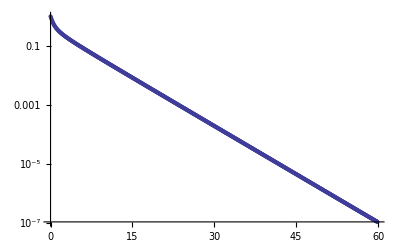

```mathematica
ListLogPlot[AbsSTableDec]
```

59.9000000000000057

P: 1.6 tEnd: 59.9000000000000057

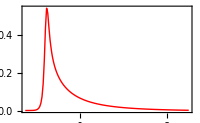

P: 1.6 tEnd: 59.9000000000000057

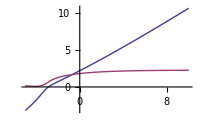

```mathematica
ReSInterpolExDec=Interpolation[ReSTableDec];
ImSInterpolExDec=Interpolation[ImSTableDec];
AbsSInterpolExDec=Interpolation[AbsSTableDec];

(*St=LogLogPlot[Abs@(AbsSInterpolExDec[t]-AbsSInterpolExDec[tmax]),{t,0.01,tmax},Frame->True,PlotRange->All,PlotStyle->{Red},PlotPoints->15,MaxRecursion->6];
(*ReImSt=Plot[{Arg[ReSInterpolExDec[t]+ⅈ*ImSInterpolExDec[t]]},{t,0.01,tmax},Frame->True,PlotRange->All,PlotStyle->{Red,Blue},PlotPoints->15,MaxRecursion->6];*)
Print["P: ", N[data0[[1,1]],2], " tEnd: ", tEnd];
Print[Show[St,ImageSize->200]];
(*Print[Show[ReImSt,ImageSize->200]];*)
*)
(*tEnd=t/.FindRoot[ImSInterpolExDec[t],{t,0.95tmax}];*)

(*If[tEnd>tmax,tEnd=tmax];*)
tEnd=tmax
res=FourierTransformationFromInterpol[ReSInterpolExDec,ImSInterpolExDec,tEnd,2^14][[1]]//Quiet;
fullres=FourierTransformationFromInterpol[ReSInterpolExDec,ImSInterpolExDec,tEnd,2^14][[1;;2]]//Quiet;

LinResSingleStep=Table[{res[[i,1]],1/π Re@res[[i,2]]},{i,1,Length@res}];
int=Interpolation[LinResSingleStep,InterpolationOrder->1];
spec=Plot[int[w],{w,wrange[[1]],wrange[[2]]},Frame->True,PlotRange->All,PlotStyle->{Red},PlotPoints->15,MaxRecursion->6];
(*Print[Show[spec]];*)
data=Cases[spec,Line[data_]:>data,-4,1][[1]];
Print["P: ", N[data0[[1,1]],2], " tEnd: ", tEnd];
Print[Show[spec,ImageSize->200]];
AppendTo[spectab,int];
AppendTo[DensityTable,Table[{data0[[1,1]],data[[i,1]],data[[i,2]]},{i,1,Length@data}]];

retab=fullres[[1,All]];
reint=Interpolation[retab];
imtab=fullres[[2,All]];
imint=Interpolation[imtab];
Print["P: ", N[data0[[1,1]],2], " tEnd: ", tEnd];
Print[Plot[{Re[ⅈ/(reint[w]+ⅈ imint[w])],Im[ⅈ/(reint[w]+ⅈ imint[w])]},{w,-5,10},PlotRange->All]];


DensityTable=Flatten[DensityTable,1];
```

```mathematica
PlotSpec2=Show[ListDensityPlot[DensityTable,PlotRange->{{0,3.34},{-5,5},All},InterpolationOrder->1,ColorFunction->(ColorData[{"SunsetColors","Reverse"}]),ClippingStyle->Automatic,ColorFunctionScaling->{-0.01,1}],AspectRatio->1,PlotRangeClipping->True,PlotRangePadding->None,RichSty[{"P/P_crit","ω"},14,0.0036,"Times"],PlotLabel->"A(ω), a_IB^-1=-2"]
```

-Graphics-

```mathematica
Export["PlotSpec2.pdf",PlotSpec2]
```

PlotSpec2.pdf

```mathematica
DensityTable
```

{{0.,-10.,0.00219575},{0.,-9.97853,0.0021993},{0.,-9.95706,0.00220285},«14064»,{3.44271483691331603,9.97687,0.0164009},{3.44271483691331603,10.,0.0163045}}

```mathematica
n=10;
ListPlot[Sort[Transpose[Drop[Transpose[Take[DensityTable,{600*n+1,600*(n+1)}]],1]],#1[[1]]<#2[[1]]&],PlotRange->{{-30,30},All},Joined->True]
```

-Graphics-

```mathematica
Show[-Graphics-,LogPlot[0.009Exp[-x*0.08],{x,0.1,60}]]
```

-Graphics-

```mathematica
Show[-Graphics-,LogLogPlot[0.77x^-0.14,{x,0.1,60}]]
```

-Graphics-

### run 2

```mathematica
folder0=NotebookDirectory[];
folder=folder0<>"/run_2/"
SetDirectory[folder];
Name=FileNames[];
```

/Users/yes/Documents/Scientific_Projects/Variational_approaches/genPolaron/mm//run_2/

```mathematica
data={};
Do[
data=Join[data,Import[Name[[n]]]];
,{n,Length[Name]}]
```

```mathematica
tTable=Transpose[data][[1]];
ReSTable=Transpose[data][[2]];
ImSTable=Transpose[data][[3]];
```

```mathematica
Name=FileNames[];


tDecay=100000;
wrange={-5,10};
DensityTable=Table[0,{0}];
spectab=Table[0,{0}];

ii=20;

data0=Import[Name[[ii]]];
tTable=Transpose[data0][[2]];
tmax=Max[tTable];
acur=-2;

ReSTable=Transpose[data0][[3]];
ImSTable=Transpose[data0][[4]];
STable=ReSTable + ⅈ *ImSTable;
AbsSTable=Abs[STable];

ReSInterpol=Interpolation[ReSTable];
ImSInterpol=Interpolation[ImSTable];
AbsSInterpol=Interpolation[AbsSTable];

ReSTableDec=Table[{tTable[[i]],Re[STable[[i]]]Exp[-tTable[[i]]/tDecay]},{i,1,Length@tTable}];
ImSTableDec=Table[{tTable[[i]],Im[STable[[i]]]Exp[-tTable[[i]]/tDecay]},{i,1,Length@tTable}];

AbsSTableDec=Table[{tTable[[i]],Abs[STable[[i]]]Exp[-tTable[[i]]/tDecay]},{i,1,Length@tTable}];
PhaseSTableDec={};
n=0;
Do[
time=tTable[[i]];
If[i>1&&Arg[STable[[i]]]<Arg[STable[[i-1]]],n++];
phase=Arg[STable[[i]]]+2*π*n;
PhaseSTableDec=Append[PhaseSTableDec,{time,phase}];
,{i,1,Length@tTable}];

ReSInterpolExDec=Interpolation[ReSTableDec];
ImSInterpolExDec=Interpolation[ImSTableDec];
AbsSInterpolExDec=Interpolation[AbsSTableDec];
PhaseSInterpolExDec=Interpolation[PhaseSTableDec];

St=LogPlot[Abs@(AbsSInterpolExDec[t]-AbsSInterpolExDec[tmax]),{t,0.01,tmax},Frame->True,PlotRange->All,PlotStyle->{Red},PlotPoints->15,MaxRecursion->6];
St=LogLogPlot[Abs@(AbsSInterpolExDec[t]),{t,0.01,tmax},Frame->True,PlotRange->All,PlotStyle->{Red},PlotPoints->15,MaxRecursion->6];
(*ReImSt=Plot[{Arg[ReSInterpolExDec[t]+ⅈ*ImSInterpolExDec[t]]},{t,0.01,tmax},Frame->True,PlotRange->All,PlotStyle->{Red,Blue},PlotPoints->15,MaxRecursion->6];*)
Print["P: ", N[data0[[1,1]],2], " tEnd: ", tEnd];
Print[Show[St,ImageSize->200]];
(*Print[Show[ReImSt,ImageSize->200]];*)

FitDecay=FindFit[Take[AbsSTableDec,-200],{a*x^α},{a,α},x]

tEnd=t/.FindRoot[ImSInterpolExDec[t],{t,0.95tmax}];

If[tEnd>tmax,tEnd=tmax];

res=FourierTransformationFromInterpol[ReSInterpolExDec,ImSInterpolExDec,tEnd,2^14][[1]]//Quiet;
fullres=FourierTransformationFromInterpol[ReSInterpolExDec,ImSInterpolExDec,tEnd,2^14][[1;;2]]//Quiet;

LinResSingleStep=Table[{res[[i,1]],1/π Re@res[[i,2]]},{i,1,Length@res}];
int=Interpolation[LinResSingleStep,InterpolationOrder->1];
(*spec=Plot[int[w],{w,wrange[[1]],wrange[[2]]},Frame->True,PlotRange->All,PlotStyle->{Red},PlotPoints->15,MaxRecursion->6];*)
(*Print[Show[spec]];*)
data=Cases[spec,Line[data_]:>data,-4,1][[1]];
(*Print["P: ", N[data0[[1,1]],2], " tEnd: ", tEnd];*)
(*Print[Show[spec,ImageSize->200]];*)
AppendTo[spectab,int];
AppendTo[DensityTable,Table[{data0[[1,1]],data[[i,1]],data[[i,2]]},{i,1,Length@data}]];

retab=fullres[[1,All]];
reint=Interpolation[retab];
imtab=fullres[[2,All]];
imint=Interpolation[imtab];
(*Print["P: ", N[data0[[1,1]],2], " tEnd: ", tEnd];
Print[Plot[{Re[ⅈ/(reint[w]+ⅈ imint[w])],Im[ⅈ/(reint[w]+ⅈ imint[w])]},{w,-5,10},PlotRange->All]];*)

DensityTable=Flatten[DensityTable,1];
```

P: 1.4 tEnd: 57.6627

-Graphics-

{a→0.752792344872001045,α→-0.057765529305818902}

```mathematica
ListPlot[PhaseSTableDec]
```

-Graphics-

```mathematica
Show[-Graphics-,LogLogPlot[a x^α/.FitDecay,{x,0.1,60}]]
```

-Graphics-

### run 7 new

```mathematica
folder0="/Users/yes/Documents/Scientific_Projects/Variational_approaches/genPolaron/data/production_data/aIBi_-4.00/";
folder=folder0<>"NGridPoints_4.00E+04/"
SetDirectory[folder];
Name=FileNames[]
```

/Users/yes/Documents/Scientific_Projects/Variational_approaches/genPolaron/data/production_data/aIBi_-4.00/NGridPoints_4.00E+04/

{paramInfo.txt,quench_aIBi_-4.00_P_0.00.dat,quench_aIBi_-4.00_P_0.07.dat,quench_aIBi_-4.00_P_0.14.dat,quench_aIBi_-4.00_P_0.21.dat,quench_aIBi_-4.00_P_0.28.dat,quench_aIBi_-4.00_P_0.36.dat,quench_aIBi_-4.00_P_0.43.dat,quench_aIBi_-4.00_P_0.50.dat,quench_aIBi_-4.00_P_0.57.dat,quench_aIBi_-4.00_P_0.64.dat,quench_aIBi_-4.00_P_0.71.dat,quench_aIBi_-4.00_P_0.78.dat,quench_aIBi_-4.00_P_0.85.dat,quench_aIBi_-4.00_P_0.92.dat,quench_aIBi_-4.00_P_0.99.dat,quench_aIBi_-4.00_P_1.07.dat,quench_aIBi_-4.00_P_1.14.dat,quench_aIBi_-4.00_P_1.21.dat,quench_aIBi_-4.00_P_1.28.dat,quench_aIBi_-4.00_P_1.35.dat,quench_aIBi_-4.00_P_1.42.dat,quench_aIBi_-4.00_P_1.49.dat,quench_aIBi_-4.00_P_1.56.dat,quench_aIBi_-4.00_P_1.63.dat,quench_aIBi_-4.00_P_1.71.dat,quench_aIBi_-4.00_P_1.78.dat,quench_aIBi_-4.00_P_1.85.dat,quench_aIBi_-4.00_P_1.92.dat,quench_aIBi_-4.00_P_1.99.dat,quench_aIBi_-4.00_P_2.06.dat,quench_aIBi_-4.00_P_2.13.dat,quench_aIBi_-4.00_P_2.20.dat,quench_aIBi_-4.00_P_2.27.dat,quench_aIBi_-4.00_P_2.34.dat,quench_aIBi_-4.00_P_2.42.dat,quench_aIBi_-4.00_P_2.49.dat,quench_aIBi_-4.00_P_2.56.dat,quench_aIBi_-4.00_P_2.63.dat,quench_aIBi_-4.00_P_2.70.dat,quench_aIBi_-4.00_P_2.77.dat}

```mathematica
data={};
Do[
data=Join[data,Import[Name[[n]]]];
,{n,2,Length[Name]}]
```

```mathematica
tTable=Transpose[data][[1]];
ReSTable=Transpose[data][[2]];
ImSTable=Transpose[data][[3]];
NphTable=Transpose[data][[6]];
```

```mathematica
Name=FileNames[];


tDecay=10000;
wrange={-10,10};
DensityTable=Table[0,{0}];
spectab=Table[0,{0}];
PowerTable={};
ZTable={};
StTable3D={};
NphTable1={};
PphTable1={};
For[ii=2,ii≤Length@Name,ii++,

data0=Import[Name[[ii]]];
Ptable=Transpose[data0][[1]];
tTable=Transpose[data0][[2]];
tmax=Max[tTable];
acur=-2;
PhaseTable=Transpose[data0][[3]];
PphTable=Transpose[data0][[4]];
P2Table=Transpose[data0][[5]];
NphTable=Transpose[data0][[6]];
ReSTable=Transpose[data0][[7]];
ImSTable=Transpose[data0][[8]];
STable=ReSTable + ⅈ *ImSTable;
AbsSTable=Abs[STable];
ReSInterpol=Interpolation[ReSTable];
ImSInterpol=Interpolation[ImSTable];
AbsSInterpol=Interpolation[AbsSTable];
ReSTableDec=Table[{tTable[[i]],Re[STable[[i]]]Exp[-tTable[[i]]/tDecay]},{i,1,Length@tTable}];
ImSTableDec=Table[{tTable[[i]],Im[STable[[i]]]Exp[-tTable[[i]]/tDecay]},{i,1,Length@tTable}];
AbsSTableDec=Table[{tTable[[i]],Abs[STable[[i]]]},{i,1,Length@tTable}];
FitAbs=FindFit[Take[AbsSTableDec,-30],{a*t^-b},{a,b},t];
PowerTable=AppendTo[PowerTable,{data0[[1,1]],b/.FitAbs}];
ZTable=AppendTo[ZTable,{data0[[1,1]],a/.FitAbs}];
StTable3D=AppendTo[StTable3D,Table[{data0[[1,1]],Log[AbsSTableDec[[i,1]]],Log[AbsSTableDec[[i,2]]]},{i,1,Length@AbsSTableDec}]];
NphTable1=AppendTo[NphTable1,Table[{tTable[[i]],NphTable[[i]]},{i,1,Length@AbsSTableDec}]];
PphTable1=AppendTo[PphTable1,Table[{tTable[[i]],PphTable[[i]]},{i,1,Length@AbsSTableDec}]];

ReSInterpolExDec=Interpolation[ReSTableDec];
ImSInterpolExDec=Interpolation[ImSTableDec];
AbsSInterpolExDec=Interpolation[AbsSTableDec];
(*St=LogLogPlot[AbsSInterpolExDec[t],{t,0.01,tmax},Frame->True,PlotRange->All,PlotStyle->{Red},PlotPoints->15,MaxRecursion->6];
Print["P: ", N[data0[[1,1]],2], " tEnd: ", tEnd];
Print[Show[St,ImageSize->200]];*)


tEnd=t/.FindRoot[ImSInterpolExDec[t],{t,0.95tmax}];

If[tEnd>tmax,tEnd=tmax];

res=FourierTransformationFromInterpol[ReSInterpolExDec,ImSInterpolExDec,tEnd,2^14][[1]]//Quiet;
fullres=FourierTransformationFromInterpol[ReSInterpolExDec,ImSInterpolExDec,tEnd,2^14][[1;;2]]//Quiet;

LinResSingleStep=Table[{res[[i,1]],1/π Re@res[[i,2]]},{i,1,Length@res}];
int=Interpolation[LinResSingleStep,InterpolationOrder->1];
spec=Plot[int[w],{w,wrange[[1]],wrange[[2]]},Frame->True,PlotRange->All,PlotStyle->{Red},PlotPoints->15,MaxRecursion->6];
(*Print[Show[spec]];*)
data=Cases[spec,Line[data_]:>data,-4,1][[1]];
(*Print["P: ", N[data0[[1,1]],2], " tEnd: ", tEnd];*)
(*Print[Show[spec,ImageSize->200]];*)
AppendTo[spectab,int];
AppendTo[DensityTable,Table[{data0[[1,1]],data[[i,1]],data[[i,2]]},{i,1,Length@data}]];

retab=fullres[[1,All]];
reint=Interpolation[retab];
imtab=fullres[[2,All]];
imint=Interpolation[imtab];
(*Print["P: ", N[data0[[1,1]],2], " tEnd: ", tEnd];
Print[Plot[{Re[ⅈ/(reint[w]+ⅈ imint[w])],Im[ⅈ/(reint[w]+ⅈ imint[w])]},{w,-5,10},PlotRange->All]];*)

];
DensityTable=Flatten[DensityTable,1];
```

InterpolatingFunction::dmval: Input value {1461.63} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-8907.86} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1160.38} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

```mathematica
PlotSpec4=Show[ListDensityPlot[DensityTable,PlotRange->{{0,3.71},{wrange[[1]],wrange[[2]]},All},InterpolationOrder->0,ColorFunction->(ColorData[{"SunsetColors","Reverse"}]),ClippingStyle->Automatic,ColorFunctionScaling->{0,1}],AspectRatio->1,PlotRangeClipping->True,PlotRangePadding->None,RichSty[{"P","ω"},14,0.0036,"Times"],PlotLabel->"A(ω), a_IB^-1=-4"]
```

-Graphics-

```mathematica
Export["/Users/yes/Downloads/SpectrumNew.pdf",PlotSpec4,AspectRatio->0.7]
Export["/Users/yes/Dowloads/SpectrumNew.png",PlotSpec4,AspectRatio->0.7]
```

/Users/yes/Downloads/Spectrum1.pdf

/Users/yes/Dowloads/Spectrum1.png

```mathematica
Show[ListPlot[PowerTable,PlotRange->{All,{0,0.6}},PlotStyle->Red],RichSty[{"P","Power-law exponent"},14,0.0036,"Times"],GridLines->{{1.2},None}]
```

-Graphics-

```mathematica
Show[ListPlot[{ZTable,Zdata},PlotRange->{All,{0,1}},PlotStyle->Red],RichSty[{"P","Z-factor"},14,0.0036,"Times"],GridLines->{{1.2},None}]
```

-Graphics-

```mathematica
gBBt=0.628;
```

```mathematica
Show[ListPlot[Pinfinity],ListPlot[PphinfFitTable,PlotStyle->Red],RichSty[{"P","P_ph(∞)"},14,0.0036,"Times"],GridLines->{{1.2},None}]
```

-Graphics-

```mathematica
Pcrit=0.918;
```

```mathematica
Show[{ListPlot[Pimpinfty]},PlotRange->{All,{0,1}},RichSty[{"P(0)","P_imp(∞)"},14,0.0036,"Times"],GridLines->{{Pcrit,Sqrt[gBBt]},{Sqrt[gBBt]}}]
```

-Graphics-

```mathematica
Show[ListPlot[MTable1],PlotRange->{All,{0,4}},RichSty[{"P","M"},14,0.0036,"Times"],GridLines->{{1.2},{1.2}}]
```

-Graphics-

### run 7 new

```mathematica
folder0="/Users/yes/Documents/Scientific_Projects/Variational_approaches/genPolaron/data/production_data/aIBi_-4.00/";
folder=folder0<>"NGridPoints_1.00E+04/"
SetDirectory[folder];
Name=FileNames[]
```

/Users/yes/Documents/Scientific_Projects/Variational_approaches/genPolaron/data/production_data/aIBi_-4.00/NGridPoints_1.00E+04/

{paramInfo.txt,quench_aIBi_-4.00_P_0.00.dat,quench_aIBi_-4.00_P_0.07.dat,quench_aIBi_-4.00_P_0.14.dat,quench_aIBi_-4.00_P_0.20.dat,quench_aIBi_-4.00_P_0.27.dat,quench_aIBi_-4.00_P_0.34.dat,quench_aIBi_-4.00_P_0.41.dat,quench_aIBi_-4.00_P_0.47.dat,quench_aIBi_-4.00_P_0.54.dat,quench_aIBi_-4.00_P_0.61.dat,quench_aIBi_-4.00_P_0.68.dat,quench_aIBi_-4.00_P_0.74.dat,quench_aIBi_-4.00_P_0.81.dat,quench_aIBi_-4.00_P_0.88.dat,quench_aIBi_-4.00_P_0.95.dat,quench_aIBi_-4.00_P_1.01.dat,quench_aIBi_-4.00_P_1.08.dat,quench_aIBi_-4.00_P_1.15.dat,quench_aIBi_-4.00_P_1.22.dat,quench_aIBi_-4.00_P_1.28.dat,quench_aIBi_-4.00_P_1.35.dat,quench_aIBi_-4.00_P_1.42.dat,quench_aIBi_-4.00_P_1.49.dat,quench_aIBi_-4.00_P_1.55.dat,quench_aIBi_-4.00_P_1.62.dat,quench_aIBi_-4.00_P_1.69.dat,quench_aIBi_-4.00_P_1.76.dat,quench_aIBi_-4.00_P_1.82.dat,quench_aIBi_-4.00_P_1.89.dat,quench_aIBi_-4.00_P_1.96.dat,quench_aIBi_-4.00_P_2.03.dat,quench_aIBi_-4.00_P_2.09.dat,quench_aIBi_-4.00_P_2.16.dat,quench_aIBi_-4.00_P_2.23.dat,quench_aIBi_-4.00_P_2.30.dat,quench_aIBi_-4.00_P_2.36.dat,quench_aIBi_-4.00_P_2.43.dat,quench_aIBi_-4.00_P_2.50.dat,quench_aIBi_-4.00_P_2.57.dat,quench_aIBi_-4.00_P_2.63.dat,quench_aIBi_-4.00_P_2.70.dat,quench_aIBi_-4.00_P_2.77.dat,quench_aIBi_-4.00_P_2.84.dat,quench_aIBi_-4.00_P_2.90.dat,quench_aIBi_-4.00_P_2.97.dat,quench_aIBi_-4.00_P_3.04.dat,quench_aIBi_-4.00_P_3.11.dat,quench_aIBi_-4.00_P_3.17.dat,quench_aIBi_-4.00_P_3.24.dat,quench_aIBi_-4.00_P_3.31.dat,quench_aIBi_-4.00_P_3.38.dat,quench_aIBi_-4.00_P_3.44.dat,quench_aIBi_-4.00_P_3.51.dat,quench_aIBi_-4.00_P_3.58.dat,quench_aIBi_-4.00_P_3.65.dat,quench_aIBi_-4.00_P_3.71.dat}

```mathematica
data={};
Do[
data=Join[data,Import[Name[[n]]]];
,{n,2,Length[Name]}]
```

```mathematica
tTable=Transpose[data][[1]];
ReSTable=Transpose[data][[2]];
ImSTable=Transpose[data][[3]];
NphTable=Transpose[data][[6]];
```

```mathematica
Name=FileNames[];


tDecay=10000;
wrange={-10,10};
DensityTable=Table[0,{0}];
spectab=Table[0,{0}];
PowerTable={};
ZTable={};
StTable3D={};
NphTable1={};
PphTable1={};
For[ii=2,ii≤Length@Name,ii++,

data0=Import[Name[[ii]]];
Ptable=Transpose[data0][[1]];
tTable=Transpose[data0][[2]];
tmax=Max[tTable];
acur=-2;
PhaseTable=Transpose[data0][[3]];
PphTable=Transpose[data0][[4]];
P2Table=Transpose[data0][[5]];
NphTable=Transpose[data0][[6]];
ReSTable=Transpose[data0][[7]];
ImSTable=Transpose[data0][[8]];
STable=ReSTable + ⅈ *ImSTable;
AbsSTable=Abs[STable];
ReSInterpol=Interpolation[ReSTable];
ImSInterpol=Interpolation[ImSTable];
AbsSInterpol=Interpolation[AbsSTable];
ReSTableDec=Table[{tTable[[i]],Re[STable[[i]]]Exp[-tTable[[i]]/tDecay]},{i,1,Length@tTable}];
ImSTableDec=Table[{tTable[[i]],Im[STable[[i]]]Exp[-tTable[[i]]/tDecay]},{i,1,Length@tTable}];
AbsSTableDec=Table[{tTable[[i]],Abs[STable[[i]]]},{i,1,Length@tTable}];
FitAbs=FindFit[Take[AbsSTableDec,-30],{a*t^-b},{a,b},t];
PowerTable=AppendTo[PowerTable,{data0[[1,1]],b/.FitAbs}];
ZTable=AppendTo[ZTable,{data0[[1,1]],a/.FitAbs}];
StTable3D=AppendTo[StTable3D,Table[{data0[[1,1]],Log[AbsSTableDec[[i,1]]],Log[AbsSTableDec[[i,2]]]},{i,1,Length@AbsSTableDec}]];
NphTable1=AppendTo[NphTable1,Table[{tTable[[i]],NphTable[[i]]},{i,1,Length@AbsSTableDec}]];
PphTable1=AppendTo[PphTable1,Table[{tTable[[i]],PphTable[[i]]},{i,1,Length@AbsSTableDec}]];

ReSInterpolExDec=Interpolation[ReSTableDec];
ImSInterpolExDec=Interpolation[ImSTableDec];
AbsSInterpolExDec=Interpolation[AbsSTableDec];
(*St=LogLogPlot[AbsSInterpolExDec[t],{t,0.01,tmax},Frame->True,PlotRange->All,PlotStyle->{Red},PlotPoints->15,MaxRecursion->6];
Print["P: ", N[data0[[1,1]],2], " tEnd: ", tEnd];
Print[Show[St,ImageSize->200]];*)


tEnd=t/.FindRoot[ImSInterpolExDec[t],{t,0.95tmax}];

If[tEnd>tmax,tEnd=tmax];

res=FourierTransformationFromInterpol[ReSInterpolExDec,ImSInterpolExDec,tEnd,2^14][[1]]//Quiet;
fullres=FourierTransformationFromInterpol[ReSInterpolExDec,ImSInterpolExDec,tEnd,2^14][[1;;2]]//Quiet;

LinResSingleStep=Table[{res[[i,1]],1/π Re@res[[i,2]]},{i,1,Length@res}];
int=Interpolation[LinResSingleStep,InterpolationOrder->1];
spec=Plot[int[w],{w,wrange[[1]],wrange[[2]]},Frame->True,PlotRange->All,PlotStyle->{Red},PlotPoints->15,MaxRecursion->6];
(*Print[Show[spec]];*)
data=Cases[spec,Line[data_]:>data,-4,1][[1]];
(*Print["P: ", N[data0[[1,1]],2], " tEnd: ", tEnd];*)
(*Print[Show[spec,ImageSize->200]];*)
AppendTo[spectab,int];
AppendTo[DensityTable,Table[{data0[[1,1]],data[[i,1]],data[[i,2]]},{i,1,Length@data}]];

retab=fullres[[1,All]];
reint=Interpolation[retab];
imtab=fullres[[2,All]];
imint=Interpolation[imtab];
(*Print["P: ", N[data0[[1,1]],2], " tEnd: ", tEnd];
Print[Plot[{Re[ⅈ/(reint[w]+ⅈ imint[w])],Im[ⅈ/(reint[w]+ⅈ imint[w])]},{w,-5,10},PlotRange->All]];*)

];
DensityTable=Flatten[DensityTable,1];
```

InterpolatingFunction::dmval: Input value {1461.63} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-8907.86} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1160.38} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

```mathematica
PlotSpec4=Show[ListDensityPlot[DensityTable,PlotRange->{{0,3.71},{wrange[[1]],wrange[[2]]},All},InterpolationOrder->0,ColorFunction->(ColorData[{"SunsetColors","Reverse"}]),ClippingStyle->Automatic,ColorFunctionScaling->{0,1}],AspectRatio->1,PlotRangeClipping->True,PlotRangePadding->None,RichSty[{"P","ω"},14,0.0036,"Times"],PlotLabel->"A(ω), a_IB^-1=-4"]
```

-Graphics-

```mathematica
Export["/Users/yes/Downloads/SpectrumNew.pdf",PlotSpec4,AspectRatio->0.7]
Export["/Users/yes/Dowloads/SpectrumNew.png",PlotSpec4,AspectRatio->0.7]
```

/Users/yes/Downloads/Spectrum1.pdf

/Users/yes/Dowloads/Spectrum1.png

```mathematica
Show[ListPlot[PowerTable,PlotRange->{All,{0,0.6}},PlotStyle->Red],RichSty[{"P","Power-law exponent"},14,0.0036,"Times"],GridLines->{{1.2},None}]
```

-Graphics-

```mathematica
Show[ListPlot[{ZTable,Zdata},PlotRange->{All,{0,1}},PlotStyle->Red],RichSty[{"P","Z-factor"},14,0.0036,"Times"],GridLines->{{1.2},None}]
```

-Graphics-

```mathematica
ListLogLinearPlot[Table[Table[{NphTable1[[ii,i,1]],NphTable1[[ii,i,2]]},{i,1,Length[NphTable1[[ii]]]}],{ii,Length[NphTable1]}],PlotStyle->Automatic(*{Blue,Blue,Blue,{Black,Thick},Red,Red}*),PlotRange->{{0.03,300},{0,1}},Joined->True,RichSty[{"t","N_ph"},14,0.0036,"Times"]]
```

-Graphics-

-Graphics-

```mathematica
Pinfinity={};
Pimpinfty={};
PphTable1={};
PimpTable1={};
P2Table1={};
MTable1={};
For[ii=2,ii≤Length@Name,ii++,

data0=Import[Name[[ii]]];
tTable=Transpose[data0][[2]];
Ptable=Transpose[data0][[1]];
PphTable=Transpose[data0][[4]];
P2Table=Transpose[data0][[5]];
Pinfinity=Append[Pinfinity,{Ptable[[1]],PphTable[[-1]]}];
Pimpinfty=Append[Pimpinfty,{Ptable[[1]],Ptable[[1]]-PphTable[[-1]]}];
MTable1=Append[MTable1,{Ptable[[1]],Ptable[[1]]/(Ptable[[1]]-PphTable[[-1]])}];
PphTable1=AppendTo[PphTable1,Table[{tTable[[i]],PphTable[[i]]},{i,1,Length@AbsSTableDec}]];
PimpTable1=AppendTo[PimpTable1,Table[{tTable[[i]],Ptable[[1]]-PphTable[[i]]},{i,1,Length@AbsSTableDec}]];
P2Table1=AppendTo[P2Table1,Table[{tTable[[i]],P2Table[[i]]},{i,1,Length@AbsSTableDec}]];

]
```

```mathematica
ListLogLogPlot[Table[Table[{PimpTable1[[ii,i,1]],PimpTable1[[ii,i,2]]},{i,1,Length[PimpTable1[[ii]]]}],{ii,Length[PimpTable1]}],PlotStyle->Automatic,PlotRange->{All,{0,4}},Joined->True,RichSty[{"t","P_imp"},14,0.0036,"Times"]]
```

-Graphics-

```mathematica
ListLogLogPlot[Table[Table[{P2Table1[[ii,i,1]],P2Table1[[ii,i,2]]},{i,1,Length[P2Table1[[ii]]]}],{ii,Length[P2Table1]}],PlotStyle->Automatic,PlotRange->{All,All},Joined->True,RichSty[{"t","P_imp"},14,0.0036,"Times"]]
```

-Graphics-

```mathematica
ListLogLinearPlot[Table[Table[{PphTable1[[ii,i,1]],PphTable1[[ii,i,2]]},{i,1,Length[PphTable1[[ii]]]}],{ii,Length[PphTable1]}],PlotStyle->Automatic,PlotRange->{All,{0,3}},Joined->True,RichSty[{"t","P_ph"},14,0.0036,"Times"]]
```

-Graphics-

```mathematica
gBBt=0.628;
Sqrt[gBBt]
```

0.792465

```mathematica
Series[Sqrt[k^2/2*(k^2/2+2gBB)],{k,0,1}]
```

√gBB k+O[k]^2

```mathematica
Show[ListPlot[Pinfinity],RichSty[{"P","P_ph(∞)"},14,0.0036,"Times"],GridLines->{{1.2},None}]
```

-Graphics-

```mathematica
Show[ListPlot[Pimpinfty],PlotRange->{All,{0,1}},RichSty[{"P(0)","P_imp(∞)"},14,0.0036,"Times"],GridLines->{{1.1207140580897519},{Sqrt[gBBt]}}]
```

-Graphics-

```mathematica
Show[ListPlot[MTable1],PlotRange->{All,All},RichSty[{"P","M"},14,0.0036,"Times"],GridLines->{{1.2},{0.87}}]
```

-Graphics-

## Spectrum from A(ω)

```mathematica
data={};
folder=NotebookDirectory[];
SetDirectory[folder];
Name=FileNames[];
data=Import[folder<>"sfDat.dat"];
datasorted=Sort[data,#1[[1]]<#2[[1]]&];
```

```mathematica
dataEn=Import[folder<>"fmEP_aIBi_-2.00.dat"];
```

```mathematica
Show[{ListDensityPlot[datasorted,PlotRange->{{0,2},{-6,0},{0,0.1}},InterpolationOrder->0,ColorFunction->(ColorData[{"SunsetColors","Reverse"}]),ClippingStyle->Automatic,ColorFunctionScaling->{-0.01,1}],
Plot[-3.8+x^2/3.,{x,0,2},PlotStyle->{White,Thick}]},AspectRatio->1,PlotRangeClipping->True,PlotRangePadding->None,RichSty[None,14,0.0036,"Times"]]
```

-Graphics-

```mathematica
n=1;
ListPlot[Sort[Transpose[Drop[Transpose[Take[datasorted,{600*n+1,600*(n+1)}]],1]],#1[[1]]<#2[[1]]&],PlotRange->{{-30,30},All},Joined->True]
```

-Graphics-